```mathematica
ClearAll[tex,tf,mf,df,primeQpos,tr,u,id, bnTab];
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
primeQpos[n_]:=If[PrimeQ[n]&&n>0,True,False]
tr:=Trace
u[m_Integer]:=1
id[m_Integer]:=Floor[1/m]
bnTab[j_]:=Table[Binomial[n,k],{n,0,j},{k,0,n}]
```

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes ANT

Arithmetic Functions

## Harmonic Numbers

```mathematica
ClearAll[r,s,t]
r[n_]:=Binomial[(n+1)!+n,n]
s[n_]:=(r[n]-1)/((n+1)!)
t[n_]:=s[n]-(n+1)Floor[s[n]/(n+1)]
```

```mathematica
t[12]
Mod[s[12],13]
```

86021/27720

86021/27720

```mathematica
HarmonicNumber[12]
```

86021/27720

```mathematica
Table[{k,(r[k]/r[k-1])/(r[k-1]/r[k-2])},{k,3,8}]//N//tf
```

3. | 11.1926
4. | 30.702
5. | 54.7155
6. | 79.124
7. | 108.368
8. | 144.098

## Highest power of prime p in n!

```mathematica
ClearAll[f]
f[n_,p_]:=Sum[Floor[n/p^i],{i,1,Ceiling[N[Log[n]]/Log[p]]}]/;p≤n
```

```mathematica
f[10,2]
f[10,3]
f[10,5]
f[10,7]
```

8

4

2

1

```mathematica
10!
```

3628800

```mathematica
2^8 3^4 5^2 7
```

3628800

## Moebius Function

### Definition

The Moebius function is defined as follows:
μ(1) = 1;
if n > 1 write n as n = ∏_(i=1)^k (p^α_i)_i and
μ(n) = (-1)^k if α_i=1
μ(n) = 0 otherwise.

#### Example

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,Divisors[60]}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
5 | -1
6 | 1
10 | 1
12 | 0
15 | 1
20 | 0
30 | -1
60 | 0

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,1,30}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
5 | -1
6 | 1
7 | -1
8 | 0
9 | 0
10 | 1
11 | -1
12 | 0
13 | -1
14 | 1
15 | 1
16 | 0
17 | -1
18 | 0
19 | -1
20 | 0
21 | 1
22 | 1
23 | -1
24 | 0
25 | 0
26 | 1
27 | 0
28 | 0
29 | -1
30 | -1

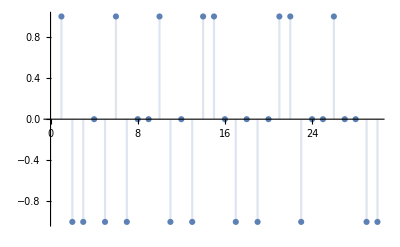

```mathematica
DiscretePlot[MoebiusMu[k],{k,30},AxesOrigin->{0,0}]
```

## Euler totient Function

### Definition

If n ≳ 1 the Euler totient ϕ(n) is defined to be the number of positive integers not exceeding n which are relatively prime to n.

Sum formula: n = ∑_(d/n) ϕ(d)

	n = ∑_(d/n) ϕ(d)
	ϕ(n) = ∑_(d/n) μ(n/d)d

Product formula: write n as n = ∏_(i=1)^k (p^α_i)_i and
	ϕ(n) = n∏_(i=1)^k (1-1/p_i)

#### Example

```mathematica
TableForm[Table[{k,EulerPhi[k]},{k,1,20}],TableHeadings->{None,{"k","ϕ[k]"}},TableAlignments->{Right}]
```

k | ϕ[k]
1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
11 | 10
12 | 4
13 | 12
14 | 6
15 | 8
16 | 8
17 | 16
18 | 6
19 | 18
20 | 8

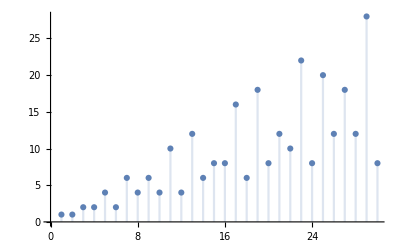

```mathematica
DiscretePlot[EulerPhi[k],{k,30},AxesOrigin->{0,0}]
```

```mathematica
Total[Map[EulerPhi[#]&,Divisors[100]]]
```

100

```mathematica
Divisors[100]
EulerPhi[100]
Total[Map[MoebiusMu[100/#]#&,Divisors[100]]]
```

{1,2,4,5,10,20,25,50,100}

40

40

## Dirichlet Multiplication ( Convolution )

### Definition

The Dirichlet convolution (f *g)(m) of two functions f(n) and g(n) is given by ∑_(d∣m) f(d) g(m/d).

#### Example

```mathematica
DirichletConvolve[MoebiusMu[n],id[n],n,12]
```

0

```mathematica
DirichletConvolve[MoebiusMu[n],u[n],n,12]
```

0

```mathematica
DirichletConvolve[MoebiusMu[n],n,n,12]
```

4

```mathematica
DirichletConvolve[MoebiusMu[n]^2 EulerPhi[n]^-1,u[n],n,12]
```

3

```mathematica
Table[{k,Log[2,DirichletConvolve[MoebiusMu[n]^2,u[n],n,k]],Total[Map[MoebiusMu[#]^2&,Divisors[k]]],2^PrimeNu[k]},{k,1,10}]//tf
```

1 | 0 | 1 | 1
2 | 1 | 2 | 2
3 | 1 | 2 | 2
4 | 1 | 2 | 2
5 | 1 | 2 | 2
6 | 2 | 4 | 4
7 | 1 | 2 | 2
8 | 1 | 2 | 2
9 | 1 | 2 | 2
10 | 2 | 4 | 4

```mathematica
DirichletConvolve[MoebiusMu[n],Log[n],n,729]//Simplify
```

Log[3]

## Chebyshev Psi

### Definition

#### Example

```mathematica
ChebyshevPsi[x_]:=Sum[MangoldtLambda[y],{y,x}]
Table[{x,ChebyshevPsi[x]//N},{x,20}]//tf
```

1 | 0.
2 | 0.693147
3 | 1.79176
4 | 2.48491
5 | 4.09434
6 | 4.09434
7 | 6.04025
8 | 6.7334
9 | 7.83201
10 | 7.83201
11 | 10.2299
12 | 10.2299
13 | 12.7949
14 | 12.7949
15 | 12.7949
16 | 13.488
17 | 16.3212
18 | 16.3212
19 | 19.2657
20 | 19.2657

```mathematica
chebyshevPsi[x_]:=x-Log[2π]-1/2 Log[1-1/x^2]-Sum[x^ZetaZero[k]/ZetaZero[k]+x^Conjugate[ZetaZero[k]]/Conjugate[ZetaZero[k]],{k,1,400}]
chebyshevPsi[x_]:=-Sum[x^ZetaZero[k]/ZetaZero[k]+x^Conjugate[ZetaZero[k]]/Conjugate[ZetaZero[k]],{k,1,400}]
Table[{x,chebyshevPsi[x]//N},{x,20}]//tf
```

1 | -0.0217662+0. ⅈ
2 | 0.0450357+0. ⅈ
3 | 0.0239878+0. ⅈ
4 | -0.0563435+0. ⅈ
5 | 0.101153+0. ⅈ
6 | -0.0827012+0. ⅈ
7 | -0.0998473+0. ⅈ
8 | 0.215926+0. ⅈ
9 | 0.117549+0. ⅈ
10 | -0.343109+0. ⅈ
11 | -0.127778+0. ⅈ
12 | 0.0677061+0. ⅈ
13 | 0.346413+0. ⅈ
14 | 0.617935+0. ⅈ
15 | -0.367124+0. ⅈ
16 | -1.04055+0. ⅈ
17 | -0.24882+0. ⅈ
18 | 0.160986+0. ⅈ
19 | 0.61506+0. ⅈ
20 | 1.14005+0. ⅈ

Numerical Methods and Tools

## Bernoulli Polynomials

### Definition / Theorem

#### Example

```mathematica
Manipulate[
Column[{Plot[BernoulliB[k,x],{x,0,1}],BernoulliB[k,x],BernoulliB[k]}],{k,1,6,1}]
```

## Approximate a Sum by an Integral

## Euler-MacLaurin Summation

### Definition / Theorem

#### Example: First Order

```mathematica
ClearAll[f]
```

```mathematica
f[k_]:=k^4+2k
f[k_]:=1/(√k)
Sum[f[k],{k,1,100}]//N
```

18.5896

```mathematica
Integrate[f[x],{x,1,5}]-1/2(f[5]-f[1])//N;
g[n_]=Integrate[f[x],{x,1,n+1},Assumptions->{n>0}]-1/2(f[n+1]-f[1])//Expand//Simplify
g[100]//N
```

(3+4 n-3 √(1+n))/(2 √(1+n))

18.55

#### Example: Second Order

```mathematica
ClearAll[f]
```

```mathematica
f[k_]:=k^4+2k
f[k_]:=1/(√k+k^2)
Sum[f[k],{k,1,4}]//N
```

0.833433

```mathematica
Integrate[f[x],{x,1,5}]-1/2(f[5]-f[1])+1/12(f'[5]-f'[1])//N;
g[n_]=Integrate[f[x],{x,1,n+1},Assumptions->{n>0}]-1/2(f[n+1]-f[1])+1/12(f'[n+1]-f'[1])//Expand//Simplify
g[4]//N//Chop
```

1/288 (87-48/((√(1+n)+(1+n)^2)^2)-(48 n)/((√(1+n)+(1+n)^2)^2)-12/(√(1+n) (√(1+n)+(1+n)^2)^2)-144/(√(1+n)+(1+n)^2)+64 √3 π-64 Log[8]+192 Log[1+1/(√(1+n))]-192 (-1)^(1/3) Log[1-(-1)^(1/3)/(√(1+n))]+192 (-1)^(2/3) Log[1+(-1)^(2/3)/(√(1+n))])

0.836458

## Euler-MacLauring Approximation

## Abel Summation

## Stieltjes Integrals

### Definition / Theorem

#### Example

## Slowly oscillating functions

### Definition / Theorem

#### Example

```mathematica
ClearAll[f]
```

```mathematica
f[x_]:=Log[Log[x]]
```

```mathematica
Limit[f[5x]/f[x],x->Infinity]
```

1

```mathematica
Limit[(x D[f[x],{x,1}])/f[x],x->Infinity]
```

0

# Notes DSC

Counting

## Definitions

### Definition / Theorem

k-Sequence of I(n)
n-Sharing of I(k)
n-Composition of k

k-Collection of I(n)
n-Partition of I(k)
n-Partition of k

#### Example

## tmp-1

```mathematica
ClearAll[f]
f[n_]:=ArrayPlot[Partition[Table[PrimeQ[k]/.{False->0,True->1},{k,n+1,n+10000}],100]]
```

```mathematica
f[1000000]
```

-Graphics-

```mathematica
-Graphics--Graphics-
```

```mathematica
PrimePi[100000]
PrimePi[7010000]-PrimePi[7000000]
PrimePi[17010000]-PrimePi[17000000]
PrimePi[100010000]-PrimePi[100000000]
```

9592

629

625

551

## tmp-2

```mathematica
Values[KeySort[PositionIndex[{2,2,1,3,3,3}]]]
```

{{3},{1,2},{4,5,6}}

```mathematica
Values[KeySort[PositionIndex[{3,1,2,2,3,3,4,3,1,3}]]]
```

{{2,9},{3,4},{1,5,6,8,10},{7}}

```mathematica
Keys[KeySort[PositionIndex[{3,1,2,2,3,3,5,3,1,3}]]]
```

{1,2,3,5}

```mathematica
KeySort[Append[KeySort[PositionIndex[{2,2,1,3,3,3,5}]],4-> {}]]
```

<|1→{3},2→{1,2},3→{4,5,6},4→{},5→{7}|>

## tmp-3: Discrete

```mathematica
?RSolve
```

```mathematica
RSolve[{a[n]-a[n-1]==n 2^n,a[0]==0,a[1]==2},a[n], n]//FullSimplify
```

{{a[n]→2+2^(1+n) (-1+n)}}

```mathematica
ClearAll[f]
f[n_]:=2+2^(1+n) (-1+n)
Table[{n,n 2^n,f[n]},{n,0,5}]//tf
```

0 | 0 | 0
1 | 2 | 2
2 | 8 | 10
3 | 24 | 34
4 | 64 | 98
5 | 160 | 258

```mathematica
ClearAll[s]
RSolve[{s[n]-s[n-1]==1/n^2,s[1]==1},s[n], n]//FullSimplify
```

{{s[n]→1/6 (π^2-6 PolyGamma[1,1+n])}}

```mathematica
ClearAll[f,g]
f[n_]:=1./n^2
g[n_]:=1./6 (π^2-6 PolyGamma[1,1+n])
Table[{n,f[n],g[n]},{n,201,212}]//tf
```

201 | 0.0000247519 | 1.63997
202 | 0.0000245074 | 1.64
203 | 0.0000242665 | 1.64002
204 | 0.0000240292 | 1.64004
205 | 0.0000237954 | 1.64007
206 | 0.0000235649 | 1.64009
207 | 0.0000233378 | 1.64011
208 | 0.0000231139 | 1.64014
209 | 0.0000228932 | 1.64016
210 | 0.0000226757 | 1.64018
211 | 0.0000224613 | 1.64021
212 | 0.0000222499 | 1.64023

```mathematica
π^2/6.
```

1.64493

```mathematica
GeneratingFunction[n,n,x];
Series[x/(1-x)^3,{x,0,10}];
CoefficientList[Series[1/(1-x)^6,{x,0,10}],x]
```

{1,6,21,56,126,252,462,792,1287,2002,3003}

```mathematica
ClearAll[f,g,k];
f[k_]:=k+2
f1[k_]=(\[DiscreteShift])_k f[k];
g[k_]:=k^2-1
g1[k_]=(\[DiscreteShift])_k g[k];
h[k_]:=f[k]g[k]
```

```mathematica
Table[{f[k],f1[k],g[k],g1[k],h[k]},{k,1,5}]//tf
```

3 | 4 | 0 | 3 | 0
4 | 5 | 3 | 8 | 12
5 | 6 | 8 | 15 | 40
6 | 7 | 15 | 24 | 90
7 | 8 | 24 | 35 | 168

```mathematica
g[k]//Expand
DiscreteShift[g[k],k]//Expand
```

-1+k^2

2 k+k^2

```mathematica
(\[DiscreteShift])_k f[k]
```

3+k

```mathematica
∆_k(\[DiscreteShift])_k g[k]
```

3+2 k

```mathematica
(\[DiscreteShift])_k∆_k g[k]
```

3+2 k

```mathematica
∆_k(f[k]g[k])//Expand
```

2+7 k+3 k^2

```mathematica
∆_k f[k](\[DiscreteShift])_k g[k]+f[k]∆_k g[k]//Expand
```

2+7 k+3 k^2

```mathematica
∆_k g[k](\[DiscreteShift])_k f[k]+g[k]∆_k f[k]//Expand
```

2+7 k+3 k^2

```mathematica
∆_k f[k](\[DiscreteShift])_k g[k]//Expand
f[k]∆_k g[k]//Expand
```

2 k+k^2

2+5 k+2 k^2

```mathematica
∆_k g[k](\[DiscreteShift])_k f[k]//Expand
g[k]∆_k f[k]//Expand
```

3+7 k+2 k^2

-1+k^2

```mathematica
(\[DiscreteShift])_k∆_k∑_k f[k]
```

3+k

```mathematica
∆_k(\[DiscreteShift])_k∑_k f[k]
```

3+k

```mathematica
∆_k∑_k (\[DiscreteShift])_k f[k]
```

3+k

```mathematica
(\[DiscreteShift])_k∑_k ∆_k f[k]
```

1+k

```mathematica
∑_k (\[DiscreteShift])_k∆_k f[k]
```

k

```mathematica
∑_k ∆_k(\[DiscreteShift])_k f[k]
```

k

```mathematica
D[f[k]g[k],k]//Expand
∆_k(f[k]g[k])//Expand
```

-1+4 k+3 k^2

2+7 k+3 k^2

```mathematica
∑_k (\[DiscreteShift])_k k^3
```

1/4 k^2 (1+k)^2

```mathematica
(\[DiscreteShift])_k∑_k k^3
```

1/4 k^2 (1+k)^2

```mathematica
5^(2)
```

25

```mathematica
4(13 12 + 13 39)
```

2652

```mathematica
52 51
```

2652

```mathematica
(4 13 12)/2652//N
```

0.235294

## tmp-4: Notation

```mathematica
<<Notation`
```

```mathematica
Notation[x_ ⊕ y_  ⟺  FactorialPower[x_,y_]]
```

```mathematica
6⊕2
```

30

```mathematica
ToBoxes[x^2,StandardForm]
```

SuperscriptBox[x,2]

```mathematica
FactorialPower[0,-4]
```

1/24

```mathematica
Sum[1/((k+1)(k+2)(k+3)(k+4)),{k,0,Infinity}]
```

1/18

```mathematica
x^UnderBar[4]
```

x^UnderBar[4]

```mathematica
Notation[BoxData[
 SuperscriptBox[x_, 
  UnderscriptBox[y_, "_"]]]  ⟺  FactorialPower[x_,y_]]
```

```mathematica
BoxData[
 SuperscriptBox[6, 
  UnderscriptBox[2, "_"]]]
```

30

```mathematica
5^UnderBar[4]
```

5^UnderBar[4]

```mathematica
FactorialPower[5,2]
```

20

5^UnderBar[4]

```mathematica
6^UnderBar[4]
```

6^UnderBar[4]

```mathematica
1/x
```

1/x

```mathematica
ab
```

ab

```mathematica
?Ket
```

```mathematica
CirclePlus[x,CenterDot[y,z]]
```

x⊕y·z

```mathematica
DownArrow[(x-2),2]
```

(-2+x)↓2

```mathematica
Notation[x_↓y_ ⟺  FunctionExpand[FactorialPower[x_,y_]]]
```

```mathematica
x↓2
```

(-1+x) x

```mathematica
(\[DiscreteShift])_x((x-1)^3)↓1//Expand
```

x^3

```mathematica
InputAliases->{"dli"->"ı"}
```

InputAliases→{dli→ı}

```mathematica
InverseFunction[f]
```

f^(-1)

```mathematica
FactorialPower[x,2]
```

x↓2

```mathematica
MakeExpression[SuperscriptBox[x_,RowBox[{"(",y_,")"}]],StandardForm]:=MakeExpression[RowBox[{FactorialPower,"[",x,",",y,"]"}],StandardForm]
```

## tmp-5:

```mathematica
?Inactive
```

```mathematica
Inactivate[2+2]
```

2+2

```mathematica
?Convolve
```

```mathematica
f[n_]:=1+n+n^2
g[n_]:=1+n+n^2
DirichletConvolve[f[n],g[n],n,m]
DiscreteConvolve[f[n],g[n],n,m]
Convolve[f[n],g[n],n,m]
```

DivisorSigma[0,m]+m DivisorSigma[0,m]+m^2 DivisorSigma[0,m]+2 DivisorSigma[1,m]+2 m DivisorSigma[1,m]+2 DivisorSigma[2,m]

DiscreteConvolve[1,1,n,m]+DiscreteConvolve[1,n,n,m]+DiscreteConvolve[1,n^2,n,m]+DiscreteConvolve[n,1,n,m]+DiscreteConvolve[n,n,n,m]+DiscreteConvolve[n,n^2,n,m]+DiscreteConvolve[n^2,1,n,m]+DiscreteConvolve[n^2,n,n,m]+DiscreteConvolve[n^2,n^2,n,m]

Convolve[1,1,n,m]+Convolve[1,n,n,m]+Convolve[1,n^2,n,m]+Convolve[n,1,n,m]+Convolve[n,n,n,m]+Convolve[n,n^2,n,m]+Convolve[n^2,1,n,m]+Convolve[n^2,n,n,m]+Convolve[n^2,n^2,n,m]

```mathematica
GeneratingFunction[n,n,x]
```

x/(-1+x)^2

```mathematica
(1+x+x^2)^2//Expand
```

1+2 x+3 x^2+2 x^3+x^4

```mathematica
CoefficientList[f[x]g[x],x]
```

{1,2,3,2,1}

```mathematica
CoefficientList[(a +b+c +d)^3,{a,b,c,d}]
```

{{{{0,0,0,1},{0,0,3,0},{0,3,0,0},{1,0,0,0}},{{0,0,3,0},{0,6,0,0},{3,0,0,0},{0,0,0,0}},{{0,3,0,0},{3,0,0,0},{0,0,0,0},{0,0,0,0}},{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,3,0},{0,6,0,0},{3,0,0,0},{0,0,0,0}},{{0,6,0,0},{6,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,3,0,0},{3,0,0,0},{0,0,0,0},{0,0,0,0}},{{3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

```mathematica
CoefficientList[(a +b+c +d)^3,b]
```

{a^3+3 a^2 c+3 a c^2+c^3+3 a^2 d+6 a c d+3 c^2 d+3 a d^2+3 c d^2+d^3,3 a^2+6 a c+3 c^2+6 a d+6 c d+3 d^2,3 a+3 c+3 d,1}

```mathematica
CoefficientList[(x+y)^1,{x,y}]
```

{{0,1},{1,0}}

```mathematica
(x+ y)^3//Expand
CoefficientList[(x+y)^3,x]
```

x^3+3 x^2 y+3 x y^2+y^3

{y^3,3 y^2,3 y,1}

```mathematica
Mod[(Binomial[4!+3,3]-1)/24,24]
```

11/6

```mathematica
(27 26 25)/6
```

2925

```mathematica
Mod[(17 43)/6,24]
```

11/6

```mathematica
(17 43)/6-120
```

11/6

```mathematica
FactorInteger[2924]
```

{{2,2},{17,1},{43,1}}

## tmp-6: Problem Set Combinatorics

### Exercise 2.

#### Method 1:

```mathematica
ClearAll[f]
f[n_]:=Module[{k,t,r},
t={0.02,0.04,0.06,0.08,0.10};
r=Accumulate[{0,9 0.02,90 0.04,900 0.06,9000 0.08,90000 0.10}];
k=Floor[Log[10,n]];
(n-(10^k-1))t[[k+1]]+r[[k+1]]
]
```

```mathematica
f[2001]
```

137.94

#### Method 2:

```mathematica
Coefficient[Series[(
.02Sum[x^k,{k,1,9}]+.04Sum[x^k,{k,10,99}]+.06Sum[x^k,{k,100,999}]+.08Sum[x^k,{k,1000,2999}])/(1-x),
{x,0,2001}],x,2001]
```

137.94

### Exercise 3.

#### Answer

```mathematica
bnTab[9]//tf
```

1 |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 |  | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 | 
1 | 9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1

```mathematica
Table[If[OddQ[Binomial[n,k]],Binomial[n,k],"-"],{n,3,31,2},{k,1,(n-1)/2}]//tf
```

3 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5 | - |  |  |  |  |  |  |  |  |  |  |  |  | 
7 | 21 | 35 |  |  |  |  |  |  |  |  |  |  |  | 
9 | - | - | - |  |  |  |  |  |  |  |  |  |  | 
11 | 55 | 165 | - | - |  |  |  |  |  |  |  |  |  | 
13 | - | - | 715 | 1287 | - |  |  |  |  |  |  |  |  | 
15 | 105 | 455 | 1365 | 3003 | 5005 | 6435 |  |  |  |  |  |  |  | 
17 | - | - | - | - | - | - | - |  |  |  |  |  |  | 
19 | 171 | 969 | - | - | - | - | - | - |  |  |  |  |  | 
21 | - | - | 5985 | 20349 | - | - | - | - | - |  |  |  |  | 
23 | 253 | 1771 | 8855 | 33649 | 100947 | 245157 | - | - | - | - |  |  |  | 
25 | - | - | - | - | - | - | 1081575 | 2042975 | - | - | - |  |  | 
27 | 351 | 2925 | - | - | - | - | 2220075 | 4686825 | 8436285 | 13037895 | - | - |  | 
29 | - | - | 23751 | 118755 | - | - | 4292145 | 10015005 | - | - | 51895935 | 67863915 | - | 
31 | 465 | 4495 | 31465 | 169911 | 736281 | 2629575 | 7888725 | 20160075 | 44352165 | 84672315 | 141120525 | 206253075 | 265182525 | 300540195

```mathematica
Map[{#[[1]],Length[#],Sum[Binomial[#[[1]],j],{j,1,(#[[1]]-1)/2}],2^(#[[1]]-1)-1}&,Map[Select[#,IntegerQ]&,Table[If[OddQ[Binomial[n,k]],Binomial[n,k],"-"],{n,3,31,2},{k,1,(n-1)/2}]]]//tf
```

3 | 1 | 3 | 3
5 | 1 | 15 | 15
7 | 3 | 63 | 63
9 | 1 | 255 | 255
11 | 3 | 1023 | 1023
13 | 3 | 4095 | 4095
15 | 7 | 16383 | 16383
17 | 1 | 65535 | 65535
19 | 3 | 262143 | 262143
21 | 3 | 1048575 | 1048575
23 | 7 | 4194303 | 4194303
25 | 3 | 16777215 | 16777215
27 | 7 | 67108863 | 67108863
29 | 7 | 268435455 | 268435455
31 | 15 | 1073741823 | 1073741823

### Exercise 4.

#### Answer

Apply Inclusion / Exclusion

```mathematica
ClearAll[f]
```

```mathematica
f[n_]:={Floor[n/3]+Floor[n/4]-Floor[n/(3 4)]-Floor[n/(3 5)]-Floor[n/(4 5)]+Floor[n/(3 4 5)]}
g[n_]:=Select[Range[n],(Mod[#,3]==0||Mod[#,4]==0)&&Mod[#,5]>0&]//Length
```

```mathematica
f[2001]
g[2001]
```

{801}

801

### Exercise 5.

```mathematica
ClearAll[f]
f[n_]:=Module[{k,t,t1,r},
t={1,2,3,4,5};
r=Accumulate[{0,9 1,90 2,900 3,9000 4,90000 5}];
k=Floor[Log[10,n]];
(n-(10^k-1))t[[k+1]]+r[[k+1]]
]
```

```mathematica
f[697]
```

1983

### Exercise 6.

### Exercise 7.

### Exercise 29.

```mathematica
ClearAll[f]
f[n_]:=Sum[(-1)^k(2^n/2^k-1)2^k,{k,1,n-1}]+2^n
f[10]
```

342

## tmp-7: Problem Set Elementary Number Theory

### Exercise 23.

```mathematica
ClearAll[f];
f[p_]:=Select[Table[{n,Mod[n^2-n,p],(n^2-n)/p},{n,1,101}],#[[2]]==0&]//tf
```

```mathematica
f[13]
```

1 | 0 | 0
13 | 0 | 12
14 | 0 | 14
26 | 0 | 50
27 | 0 | 54
39 | 0 | 114
40 | 0 | 120
52 | 0 | 204
53 | 0 | 212
65 | 0 | 320
66 | 0 | 330
78 | 0 | 462
79 | 0 | 474
91 | 0 | 630
92 | 0 | 644

## tmp-8: Hypergeometric Functions

```mathematica
HypergeometricPFQ[{1},{1},z]
HypergeometricPFQ[{1,1},{1},z]
HypergeometricPFQ[{1,2},{1},z]
Series[HypergeometricPFQ[{1,3},{1},z],{z,0,8}]
Series[z HypergeometricPFQ[{1,1},{2},-z],{z,0,8}]
z HypergeometricPFQ[{1,1},{2},-z]
Series[Log[1+z],{z,0,8}]
z HypergeometricPFQ[{1/2,1/2},{3/2},z^2]
```

ⅇ^z

1/(1-z)

1/(-1+z)^2

1+3 z+6 z^2+10 z^3+15 z^4+21 z^5+28 z^6+36 z^7+45 z^8+O[z]^9

z-z^2/2+z^3/3-z^4/4+z^5/5-z^6/6+z^7/7-z^8/8+O[z]^9

Log[1+z]

z-z^2/2+z^3/3-z^4/4+z^5/5-z^6/6+z^7/7-z^8/8+O[z]^9

ArcSin[z]

## tmp: Generating Function Integer Partitions

```mathematica
Series[Product[1/(1-z^(k+1)),{k,0,Infinity}],{z,0,11}]
Series[Product[1/(1-z^(k+1)),{k,0,Infinity}] 1/(1-z),{z,0,11}]
```

1+z+2 z^2+3 z^3+5 z^4+7 z^5+11 z^6+15 z^7+22 z^8+30 z^9+42 z^10+56 z^11+O[z]^12

1+2 z+4 z^2+7 z^3+12 z^4+19 z^5+30 z^6+45 z^7+67 z^8+97 z^9+139 z^10+195 z^11+O[z]^12

```mathematica
PartitionsP[10]
```

42

```mathematica
Series[1/(1-z^1)1/(1-z^2),{z,0,10}]
Series[Product[1/(1-z^(k+1)),{k,0,4}],{z,0,5}]
```

1+z+2 z^2+2 z^3+3 z^4+3 z^5+4 z^6+4 z^7+5 z^8+5 z^9+6 z^10+O[z]^11

1+z+2 z^2+3 z^3+5 z^4+7 z^5+O[z]^6

```mathematica
Expand[Sum[x^k,{k,0,9}]Sum[x^k,{k,0,9,2}] Sum[x^k,{k,0,9,3}] Sum[x^k,{k,0,9,4}] Sum[x^k,{k,0,9,5}]]
```

1+x+2 x^2+3 x^3+5 x^4+7 x^5+10 x^6+13 x^7+18 x^8+23 x^9+27 x^10+34 x^11+39 x^12+46 x^13+51 x^14+57 x^15+61 x^16+66 x^17+67 x^18+69 x^19+69 x^20+67 x^21+66 x^22+61 x^23+57 x^24+51 x^25+46 x^26+39 x^27+34 x^28+27 x^29+23 x^30+18 x^31+13 x^32+10 x^33+7 x^34+5 x^35+3 x^36+2 x^37+x^38+x^39

## tmp:

```mathematica
ClearAll[f]
f[n_]:=Mod[(Binomial[(n+1)!+n,n]-1)/((n+1)!),n+1]
Table[{k,f[k],f[k]//N},{k,1,8}]//tf
```

1 | 1 | 1.
2 | 3/2 | 1.5
3 | 11/6 | 1.83333
4 | 25/12 | 2.08333
5 | 137/60 | 2.28333
6 | 49/20 | 2.45
7 | 363/140 | 2.59286
8 | 761/280 | 2.71786

```mathematica
ⅇ//N
```

2.71828

```mathematica
Mod[3^10,11]
Mod[7^EulerPhi[12],12]
```

1

1

```mathematica
ClearAll[f];
f[p_]:=Select[Table[{n,Mod[n^2-n,p],(n^2-n)/p},{n,1,101}],#[[2]]==0&]//tf
```

```mathematica
f[13]
```

1 | 0 | 0
13 | 0 | 12
14 | 0 | 14
26 | 0 | 50
27 | 0 | 54
39 | 0 | 114
40 | 0 | 120
52 | 0 | 204
53 | 0 | 212
65 | 0 | 320
66 | 0 | 330
78 | 0 | 462
79 | 0 | 474
91 | 0 | 630
92 | 0 | 644

```mathematica
-Sum[(-1)^n/n^(2/5),{n,1,Infinity}]
Zeta[2/5]
```

-(-1+2^(3/5)) Zeta[2/5]

Zeta[2/5]

```mathematica
ClearAll[a]
RSolve[{a[n]==a[n-1] n+(n-1)!,a[1]==1},a[n],n]
```

```mathematica
ClearAll[a]
RSolve[{a[n]==a[n-1] n^2+((n-1)!)^2,a[1]==1},a[n],n]//FullSimplify
```

{{a[n]→1/6 Pochhammer[1,n]^2 (π^2-6 PolyGamma[1,1+n])}}

```mathematica
a[n_]:=Pochhammer[1,n] (EulerGamma+PolyGamma[0,1+n])/n!
a[n_]:=(1/6 Pochhammer[1,n]^2 (π^2-6 PolyGamma[1,1+n]))/(n!)^2
b[n_]:=Sum[1/k^2,{k,1,n}]
Table[{n,a[n],b[n]},{n,1,5}]//tf//N
Limit[a[n],n->Infinity]
```

1. | 1. | 1.
2. | 1.25 | 1.25
3. | 1.36111 | 1.36111
4. | 1.42361 | 1.42361
5. | 1.46361 | 1.46361

π^2/6

```mathematica
18435599767349200867866/10^24//N
```

0.0184356

```mathematica
x=Log[10.]/Log[2] 24
```

79.7263

```mathematica
2^x
```

1.×10^24

```mathematica
2^80
```

1208925819614629174706176

```mathematica
2^79
```

604462909807314587353088

```mathematica
ClearAll[x]
```

```mathematica
FullSimplify[Binomial[(n+2)!+n+1,n+1]/((n+2)!)-Binomial[(n+1)!+n,n]/((n+1)!),Assumptions->{n ϵ Integers, n>0}]
```

-Binomial[n+Gamma[2+n],n]/Gamma[2+n]+Binomial[1+n+Gamma[3+n],1+n]/Gamma[3+n]

```mathematica
Sum[Binomial[n,k],{k,0,m}]//Simplify
```

2^n-Binomial[n,1+m] Hypergeometric2F1[1,1+m-n,2+m,-1]

```mathematica
f[n_,m_]:=2^n-Binomial[n,1+m] Hypergeometric2F1[1,1+m-n,2+m,-1]
bnTab[10]//tf
```

1 |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  |  |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 |  |  | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 |  | 
1 | 9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 
1 | 10 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1

```mathematica
Expand[((n+1)^4-6 (n+1)^3+23(n+1)^2-18( n+1)+24)/24,n]
```

1+(7 n)/12+(11 n^2)/24-n^3/12+n^4/24

```mathematica
Table[{n,f[n,4],1+(7 n)/12+(11 n^2)/24-n^3/12+n^4/24},{n,0,10}]//tf
```

0 | 1 | 1
1 | 2 | 2
2 | 4 | 4
3 | 8 | 8
4 | 16 | 16
5 | 31 | 31
6 | 57 | 57
7 | 99 | 99
8 | 163 | 163
9 | 256 | 256
10 | 386 | 386

```mathematica
Binomial[-3,5]
```

-21

```mathematica
Gamma'[1]/Gamma[1]
```

-EulerGamma

```mathematica
Gamma'[3/2]/Gamma[3/2]
```

PolyGamma[0,3/2]

```mathematica
Zeta'[0]/Zeta[0]
```

Log[2 π]

```mathematica
N[Zeta[3]/π^3,80]
```

0.038768179602916798941119890318721149806234568039552579223126762123777137012286855

```mathematica
Zeta[3]//N
```

1.20206

```mathematica
GCD[1100,LCM[100,1000]]
```

100

```mathematica
2924/24.
Mod[2924/24,4]
```

121.833

11/6

```mathematica
121.83333333333333 6 4
```

2924.